```mathematica
Clear["Global`*"]
```

```mathematica
smatrix=Import["/home/r-matrixsuperconductor/Desktop/NSNSNSNSN/NSNSNSNSN_Smatrix_from_Tmatrix.mx"]/.{x[1]->x1,x[2]->x2,x[3]->x3,x[4]->x4,x[5]->x5,x[6]->x6,x[7]->x7,x[8]->x8};
rppLL=smatrix[[1,1]];
rphLL=smatrix[[1,2]];
tppLR=smatrix[[1,3]];
tphLR=smatrix[[1,4]];
rhpLL=smatrix[[2,1]];
rhhLL=smatrix[[2,2]];
thpLR=smatrix[[2,3]];
thhLR=smatrix[[2,4]];
tppRL=smatrix[[3,1]];
tphRL=smatrix[[3,2]];
rppRR=smatrix[[3,3]];
rphRR=smatrix[[3,4]];
thpRL=smatrix[[4,1]];
thhRL=smatrix[[4,2]];
rhpRR=smatrix[[4,3]];
rhhRR=smatrix[[4,4]];
NpL[e_]=1/(1+Exp[(e+νL)/τ]);
NhL[e_]=1/(1+Exp[(e-νL)/τ]);
NpR[e_]=1/(1+Exp[(e+νR)/τ]);
NhR[e_]=1/(1+Exp[(e-νR)/τ]);
FpL[e_]=1-NpL[e];
FhL[e_]=1-NhL[e];
FpR[e_]=1-NpR[e];
FhR[e_]=1-NhR[e];
x2=x1+ls1;
x3=x2+ln1;
x4=x3+ls2;
x5=x4+ln2;
x6=x5+ls3;
x7=x6+ln3;
x8=x7+ls4;
qp=Sqrt[2*(EF+e)];
qh=Sqrt[2*(EF-e)];
kp=Sqrt[2*(EF+Sqrt[e^2-DD^2])];
kh=Sqrt[2*(EF-Sqrt[e^2-DD^2])];    
u=Sqrt[(1+Sqrt[e^2-DD^2]/e)/2];
v=Sqrt[(1-Sqrt[e^2-DD^2]/e)/2];
x1=-2100;
ls1=200;
ls2=200;
ls3=200;
ls4=200;
ln1=800;
ln2=1800;
ln3=800;
EF=0.001307;
DD=0.00053814;
mL=1;
mR=1;
hbar=1;
νL=0;
νR=0;
τ=1/13876;(*the number in the denominator is beta:=k_B*T*)
```

```mathematica
energies=N[Table[1*10^-7*i+0.00008,{i,0,200}]];
```

```mathematica
i=100;
1*10^-7*i+0.00008
```

0.00009

## pp shot noise

```mathematica
Spp=(mL*mR)/(π^2*hbar^4)(FpL[e]*NpL[e]((-Abs[N[rhpLL]]^2+Abs[N[rppLL]]^2-1)(-Abs[N[thpRL]]^2+Abs[N[tppRL]]^2))+FpR[e]*NpR[e]((-Abs[N[rhpRR]]^2+Abs[N[rppRR]]^2-1)(-Abs[N[thpLR]]^2+Abs[N[tppLR]]^2))+(FpL[e]*NpR[e]+FpR[e]*NpL[e])(Re[N[rhpLL]*N[rhpRR]*Conjugate[N[thpLR]]*Conjugate[N[thpRL]]]-Re[Conjugate[N[rhpLL]]*Conjugate[N[rppRR]]*N[tppRL]*N[thpLR]]+Re[N[rppLL]*N[rppRR]*Conjugate[N[tppLR]]*Conjugate[N[tppRL]]]-Re[Conjugate[N[rppLL]]*Conjugate[N[rhpRR]]*N[thpRL]*N[tppLR]]));
```

```mathematica
ppterm1[e_]=((-Abs[N[rhpLL]]^2+Abs[N[rppLL]]^2-1)(-Abs[N[thpRL]]^2+Abs[N[tppRL]]^2));
ppterm2[e_]=((-Abs[N[rhpRR]]^2+Abs[N[rppRR]]^2-1)(-Abs[N[thpLR]]^2+Abs[N[tppLR]]^2));
ppterm3[e_]=(Re[N[rhpLL]*N[rhpRR]*Conjugate[N[thpLR]]*Conjugate[N[thpRL]]]-Re[Conjugate[N[rhpLL]]*Conjugate[N[rppRR]]*N[tppRL]*N[thpLR]]+Re[N[rppLL]*N[rppRR]*Conjugate[N[tppLR]]*Conjugate[N[tppRL]]]-Re[Conjugate[N[rppLL]]*Conjugate[N[rhpRR]]*N[thpRL]*N[tppLR]]);
```

```mathematica
i=100;
e=1*10^-7*i+0.00008;
((-Abs[N[rhpLL]]^2+Abs[N[rppLL]]^2-1)(-Abs[N[thpRL]]^2+Abs[N[tppRL]]^2))
((-Abs[N[rhpRR]]^2+Abs[N[rppRR]]^2-1)(-Abs[N[thpLR]]^2+Abs[N[tppLR]]^2))
(Re[N[rhpLL]*N[rhpRR]*Conjugate[N[thpLR]]*Conjugate[N[thpRL]]]-Re[Conjugate[N[rhpLL]]*Conjugate[N[rppRR]]*N[tppRL]*N[thpLR]]+Re[N[rppLL]*N[rppRR]*Conjugate[N[tppLR]]*Conjugate[N[tppRL]]]-Re[Conjugate[N[rppLL]]*Conjugate[N[rhpRR]]*N[thpRL]*N[tppLR]])
e=.
```

0.0407543

0.0407543

0.140665

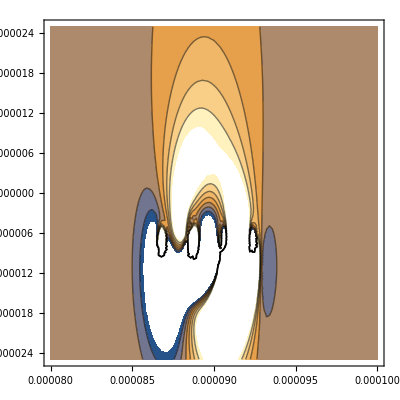

-Graphics-

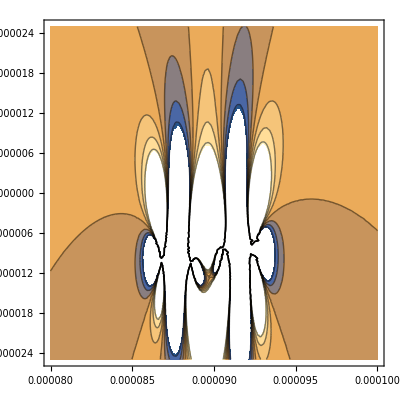

```mathematica
e=er+I*ei;
ContourPlot[((-Abs[N[rhpLL]]^2+Abs[N[rppLL]]^2-1)(-Abs[N[thpRL]]^2+Abs[N[tppRL]]^2)),{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[((-Abs[N[rhpRR]]^2+Abs[N[rppRR]]^2-1)(-Abs[N[thpLR]]^2+Abs[N[tppLR]]^2)),{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[(Re[N[rhpLL]*N[rhpRR]*Conjugate[N[thpLR]]*Conjugate[N[thpRL]]]-Re[Conjugate[N[rhpLL]]*Conjugate[N[rppRR]]*N[tppRL]*N[thpLR]]+Re[N[rppLL]*N[rppRR]*Conjugate[N[tppLR]]*Conjugate[N[tppRL]]]-Re[Conjugate[N[rppLL]]*Conjugate[N[rhpRR]]*N[thpRL]*N[tppLR]]),{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
e=.
```

## hh shot noise

```mathematica
Shh=(mL*mR)/(π^2*hbar^4)(FhL[e]*NhL[e]((Abs[N[rhhLL]]^2-Abs[N[rphLL]]^2-1)(Abs[N[thhRL]]^2-Abs[N[tphRL]]^2))+FhR[e]*NhR[e]((Abs[N[rhhRR]]^2-Abs[N[rphRR]]^2-1)(Abs[N[thhLR]]^2-Abs[N[tphLR]]^2))+(FhL[e]*NhR[e]+FhR[e]*NhL[e])(Re[N[rhhLL]*N[rhhRR]*Conjugate[N[thhLR]]*Conjugate[N[thhRL]]]-Re[Conjugate[N[rhhLL]]*Conjugate[N[rphRR]]*N[tphRL]*N[thhLR]]+Re[N[rphLL]*N[rphRR]*Conjugate[N[tphLR]]*Conjugate[N[tphRL]]]-Re[Conjugate[N[rphLL]]*Conjugate[N[rhhRR]]*N[thhRL]*N[tphLR]]));
```

```mathematica
hhterm1=((Abs[N[rhhLL]]^2-Abs[N[rphLL]]^2-1)(Abs[N[thhRL]]^2-Abs[N[tphRL]]^2));
hhterm2=((Abs[N[rhhRR]]^2-Abs[N[rphRR]]^2-1)(Abs[N[thhLR]]^2-Abs[N[tphLR]]^2));
hhterm3=(Re[N[rhhLL]*N[rhhRR]*Conjugate[N[thhLR]]*Conjugate[N[thhRL]]]-Re[Conjugate[N[rhhLL]]*Conjugate[N[rphRR]]*N[tphRL]*N[thhLR]]+Re[N[rphLL]*N[rphRR]*Conjugate[N[tphLR]]*Conjugate[N[tphRL]]]-Re[Conjugate[N[rphLL]]*Conjugate[N[rhhRR]]*N[thhRL]*N[tphLR]]);
```

```mathematica
i=100;
e=1*10^-7*i+0.00008;
((Abs[N[rhhLL]]^2-Abs[N[rphLL]]^2-1)(Abs[N[thhRL]]^2-Abs[N[tphRL]]^2))
((Abs[N[rhhRR]]^2-Abs[N[rphRR]]^2-1)(Abs[N[thhLR]]^2-Abs[N[tphLR]]^2))
(Re[N[rhhLL]*N[rhhRR]*Conjugate[N[thhLR]]*Conjugate[N[thhRL]]]-Re[Conjugate[N[rhhLL]]*Conjugate[N[rphRR]]*N[tphRL]*N[thhLR]]+Re[N[rphLL]*N[rphRR]*Conjugate[N[tphLR]]*Conjugate[N[tphRL]]]-Re[Conjugate[N[rphLL]]*Conjugate[N[rhhRR]]*N[thhRL]*N[tphLR]])
e=.
```

0.0508826

0.0508826

0.145472

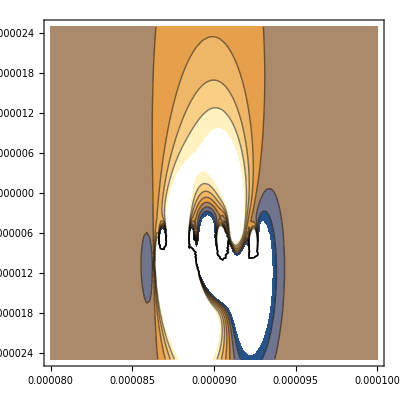

-Graphics-

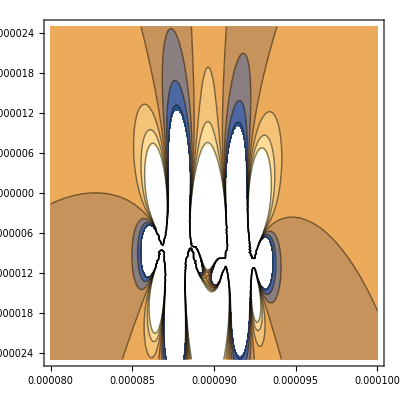

```mathematica
e=er+I*ei;
ContourPlot[((Abs[N[rhhLL]]^2-Abs[N[rphLL]]^2-1)(Abs[N[thhRL]]^2-Abs[N[tphRL]]^2)),{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[((Abs[N[rhhRR]]^2-Abs[N[rphRR]]^2-1)(Abs[N[thhLR]]^2-Abs[N[tphLR]]^2)),{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[(Re[N[rhhLL]*N[rhhRR]*Conjugate[N[thhLR]]*Conjugate[N[thhRL]]]-Re[Conjugate[N[rhhLL]]*Conjugate[N[rphRR]]*N[tphRL]*N[thhLR]]+Re[N[rphLL]*N[rphRR]*Conjugate[N[tphLR]]*Conjugate[N[tphRL]]]-Re[Conjugate[N[rphLL]]*Conjugate[N[rhhRR]]*N[thhRL]*N[tphLR]]),{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
e=.
```

## ph shot noise

```mathematica
Sph=(mL*mR)/(π^2*hbar^4)((FhL[e]*NpL[e]+FpL[e]*NhL[e])(Re[N[rhhLL]*Conjugate[N[rhpLL]]*N[thpRL]*Conjugate[N[thhRL]]]-Re[N[rhhLL]*Conjugate[N[rhpLL]]*Conjugate[N[tphLR]]*N[tppRL]]-Re[N[rphLL]*Conjugate[N[rppLL]]*Conjugate[N[thhRL]]*N[thpRL]]+Re[N[rphLL]*Conjugate[N[rppLL]]*N[tppRL]*Conjugate[N[tphRL]]])+(FhR[e]*NpR[e]+FpR[e]*NhR[e])(Re[N[rhhRR]*Conjugate[N[rhpRR]]*N[thpLR]*Conjugate[N[thhLR]]]-Re[N[rhhRR]*Conjugate[N[rhpRR]]*Conjugate[N[tphLR]]*N[tppLR]]-Re[N[rphRR]*Conjugate[N[rppRR]]*Conjugate[N[thhLR]]*N[thpLR]]+Re[N[rphRR]*Conjugate[N[rppRR]]*N[tppLR]*Conjugate[N[tphLR]]])+(FhL[e]*NpR[e]+FpR[e]*NhL[e])(Re[N[rhhLL]*N[rhpRR]*Conjugate[N[thpLR]]*Conjugate[N[thhRL]]]-Re[Conjugate[N[rhhLL]]*Conjugate[N[rppRR]]*N[tphRL]*N[thpLR]]+Re[N[rphLL]*N[rppRR]*Conjugate[N[tppLR]]*Conjugate[N[tphRL]]]-Re[Conjugate[N[rphLL]]*Conjugate[N[rhpRR]]*N[thhRL]*N[tppLR]])+(FpL[e]*NhR[e]+FhR[e]*NpL[e])(Re[N[rhpLL]*N[rhhRR]*Conjugate[N[thhLR]]*Conjugate[N[thpRL]]]-Re[Conjugate[N[rhpLL]]*Conjugate[N[rphRR]]*N[tppRL]*N[thhLR]]+Re[N[rppLL]*N[rphRR]*Conjugate[N[tphLR]]*Conjugate[N[tppRL]]]-Re[Conjugate[N[rppLL]]*Conjugate[N[rhhRR]]*N[thpRL]*N[tphLR]]))
```

```mathematica
phterm1=(Re[N[rhhLL]*Conjugate[N[rhpLL]]*N[thpRL]*Conjugate[N[thhRL]]]-Re[N[rhhLL]*Conjugate[N[rhpLL]]*Conjugate[N[tphLR]]*N[tppRL]]-Re[N[rphLL]*Conjugate[N[rppLL]]*Conjugate[N[thhRL]]*N[thpRL]]+Re[N[rphLL]*Conjugate[N[rppLL]]*N[tppRL]*Conjugate[N[tphRL]]])
phterm2=(Re[N[rhhRR]*Conjugate[N[rhpRR]]*N[thpLR]*Conjugate[N[thhLR]]]-Re[N[rhhRR]*Conjugate[N[rhpRR]]*Conjugate[N[tphLR]]*N[tppLR]]-Re[N[rphRR]*Conjugate[N[rppRR]]*Conjugate[N[thhLR]]*N[thpLR]]+Re[N[rphRR]*Conjugate[N[rppRR]]*N[tppLR]*Conjugate[N[tphLR]]])
phterm3=(Re[N[rhhLL]*N[rhpRR]*Conjugate[N[thpLR]]*Conjugate[N[thhRL]]]-Re[Conjugate[N[rhhLL]]*Conjugate[N[rppRR]]*N[tphRL]*N[thpLR]]+Re[N[rphLL]*N[rppRR]*Conjugate[N[tppLR]]*Conjugate[N[tphRL]]]-Re[Conjugate[N[rphLL]]*Conjugate[N[rhpRR]]*N[thhRL]*N[tppLR]])
phterm4=(Re[N[rhpLL]*N[rhhRR]*Conjugate[N[thhLR]]*Conjugate[N[thpRL]]]-Re[Conjugate[N[rhpLL]]*Conjugate[N[rphRR]]*N[tppRL]*N[thhLR]]+Re[N[rppLL]*N[rphRR]*Conjugate[N[tphLR]]*Conjugate[N[tppRL]]]-Re[Conjugate[N[rppLL]]*Conjugate[N[rhhRR]]*N[thpRL]*N[tphLR]])
```

```mathematica
i=100;
e=1*10^-7*i+0.00008;
(Re[N[rhhLL]*Conjugate[N[rhpLL]]*N[thpRL]*Conjugate[N[thhRL]]]-Re[N[rhhLL]*Conjugate[N[rhpLL]]*Conjugate[N[tphLR]]*N[tppRL]]-Re[N[rphLL]*Conjugate[N[rppLL]]*Conjugate[N[thhRL]]*N[thpRL]]+Re[N[rphLL]*Conjugate[N[rppLL]]*N[tppRL]*Conjugate[N[tphRL]]])
(Re[N[rhhRR]*Conjugate[N[rhpRR]]*N[thpLR]*Conjugate[N[thhLR]]]-Re[N[rhhRR]*Conjugate[N[rhpRR]]*Conjugate[N[tphLR]]*N[tppLR]]-Re[N[rphRR]*Conjugate[N[rppRR]]*Conjugate[N[thhLR]]*N[thpLR]]+Re[N[rphRR]*Conjugate[N[rppRR]]*N[tppLR]*Conjugate[N[tphLR]]])
(Re[N[rhhLL]*N[rhpRR]*Conjugate[N[thpLR]]*Conjugate[N[thhRL]]]-Re[Conjugate[N[rhhLL]]*Conjugate[N[rppRR]]*N[tphRL]*N[thpLR]]+Re[N[rphLL]*N[rppRR]*Conjugate[N[tppLR]]*Conjugate[N[tphRL]]]-Re[Conjugate[N[rphLL]]*Conjugate[N[rhpRR]]*N[thhRL]*N[tppLR]])
(Re[N[rhpLL]*N[rhhRR]*Conjugate[N[thhLR]]*Conjugate[N[thpRL]]]-Re[Conjugate[N[rhpLL]]*Conjugate[N[rphRR]]*N[tppRL]*N[thhLR]]+Re[N[rppLL]*N[rphRR]*Conjugate[N[tphLR]]*Conjugate[N[tppRL]]]-Re[Conjugate[N[rppLL]]*Conjugate[N[rhhRR]]*N[thpRL]*N[tphLR]])
e=.
```

-0.126577

-0.126577

-0.000328871

-0.000328871

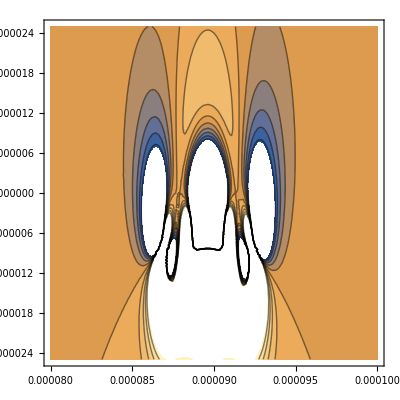

-Graphics-

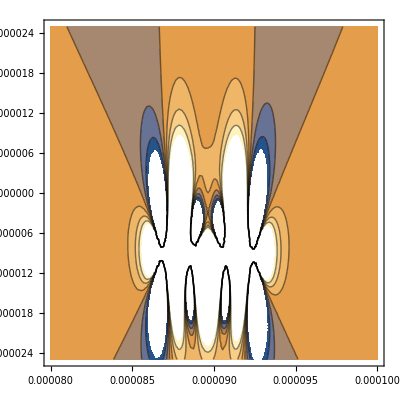

-Graphics-

```mathematica
e=er+I*ei;
ContourPlot[(Re[N[rhhLL]*Conjugate[N[rhpLL]]*N[thpRL]*Conjugate[N[thhRL]]]-Re[N[rhhLL]*Conjugate[N[rhpLL]]*Conjugate[N[tphLR]]*N[tppRL]]-Re[N[rphLL]*Conjugate[N[rppLL]]*Conjugate[N[thhRL]]*N[thpRL]]+Re[N[rphLL]*Conjugate[N[rppLL]]*N[tppRL]*Conjugate[N[tphRL]]]),{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[(Re[N[rhhRR]*Conjugate[N[rhpRR]]*N[thpLR]*Conjugate[N[thhLR]]]-Re[N[rhhRR]*Conjugate[N[rhpRR]]*Conjugate[N[tphLR]]*N[tppLR]]-Re[N[rphRR]*Conjugate[N[rppRR]]*Conjugate[N[thhLR]]*N[thpLR]]+Re[N[rphRR]*Conjugate[N[rppRR]]*N[tppLR]*Conjugate[N[tphLR]]]),{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[(Re[N[rhhLL]*N[rhpRR]*Conjugate[N[thpLR]]*Conjugate[N[thhRL]]]-Re[Conjugate[N[rhhLL]]*Conjugate[N[rppRR]]*N[tphRL]*N[thpLR]]+Re[N[rphLL]*N[rppRR]*Conjugate[N[tppLR]]*Conjugate[N[tphRL]]]-Re[Conjugate[N[rphLL]]*Conjugate[N[rhpRR]]*N[thhRL]*N[tppLR]]),{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
ContourPlot[(Re[N[rhpLL]*N[rhhRR]*Conjugate[N[thhLR]]*Conjugate[N[thpRL]]]-Re[Conjugate[N[rhpLL]]*Conjugate[N[rphRR]]*N[tppRL]*N[thhLR]]+Re[N[rppLL]*N[rphRR]*Conjugate[N[tphLR]]*Conjugate[N[tppRL]]]-Re[Conjugate[N[rppLL]]*Conjugate[N[rhhRR]]*N[thpRL]*N[tphLR]]),{er,0.00008,0.0001},{ei,-2.5*10^-6,2.5*10^-6}]
e=.
```